```mathematica
ClearAll["Global`*"];

G = 6.67 * 10^-11;

Mz = 5.96 * 10^24;

m=1500;

FG = G * (m*Mz)/R^2;

Fod = (m * v^2) /R;

Ek = (m * v^2) / 2;

EpR = -G * (m * Mz) / R;
```

```mathematica
r1 = Solve[Fod==FG,v];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
Ec[R_]=Ek+EpR/.r1[[2,1]];
```

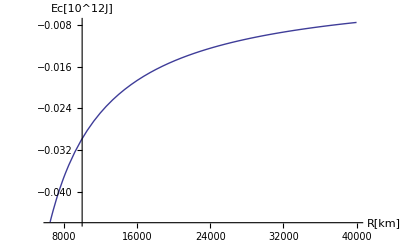

```mathematica
Plot[Ec[R*10^3]/10^12, {R,6500,40000},
AxesLabel->{"R[km]","Ec[10^12J]"}]
```